```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fPreferredSelector[aNumber_,n_Integer]:=If[aNumber==1,{n,2},If[aNumber==n,{n-1,1},{aNumber-1,aNumber+1}]]
fPreferredBinary[aNumber_,n_Integer]:=If[#==1,1,0]&/@Mod[Abs[Range@n-aNumber],n-2]
fProposalProbabilities[aNumber_,n_Integer,epsilon_]:=Module[{lPreferredSelector=fPreferredBinary[aNumber,n]},(0.5-(epsilon/2)) lPreferredSelector +(epsilon/n)ConstantArray[1,n]]
toPiecewise[wts_,x_]:=Piecewise[MapIndexed[{#1,x==#2[[1]]}&,wts]]
fSelectNext[aNumber_,n_Integer,epsilon_]:=Module[{wts=fProposalProbabilities[aNumber,n,epsilon],f},f=ProbabilityDistribution[toPiecewise[wts,x],{x,1,n,1}];RandomVariate[f,{1}]][[1]]
fGenerateSamples[numSamples_,aStartNumber_,n_Integer,epsilon_]:=NestList[fSelectNext[#,n,epsilon]&,aStartNumber,numSamples]
fGenerateTransitions[maxSamples_Integer,n_Integer,epsilon_]:=Table[RandomVariate[ProbabilityDistribution[toPiecewise[fProposalProbabilities[i,n,epsilon],x],{x,1,n,1}],{maxSamples}],{i,1,n,1}]
fChain[numChains_Integer,numSamples_Integer,n_Integer,epsilon_]:=Module[{lAllTransitions=fGenerateTransitions[numChains numSamples,n,epsilon],lSteps=Range@(numChains numSamples),lTotal},lTotal=FoldList[fStep[#1,#2,lAllTransitions]&,RandomInteger[{1,n}],lSteps];Partition[lTotal,numSamples]]
fStep[aCurrentNumber_Integer,aStepNumber_Integer,lSamples__]:=lSamples[[aCurrentNumber,aStepNumber]]
fVarianceEstimator[n_Integer,numChains_Integer,numSamples_,epsilon_]:=Variance[Mean/@fChain[numChains,numSamples,n,epsilon]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{5,9.45498},{10,19.4456},{15,31.1159},{20,41.5393},{25,51.6206},{30,62.8856},{35,72.1921},{40,81.3217}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

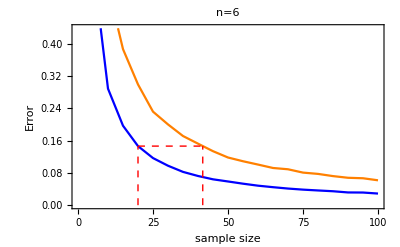

```mathematica
vSampleSize=Table[i,{i,5,100,5}];
lVariance=ParallelTable[fVarianceEstimator[6,10000,i,1],{i,vSampleSize}];
lVariance2=ParallelTable[fVarianceEstimator[6,10000,i,0],{i,vSampleSize}];
f2=Interpolation[Thread[{vSampleSize,lVariance}]];
h2=Interpolation[Thread[{vSampleSize,lVariance2}]];
l6=Table[{n,NSolve[h1[x]==f1[n],x][[1,1,2]]},{n,5,40,5}]
aSolve=NSolve[h2[x]==f2[20],x][[1,1,2]];
bSolve=aSolve;
g1=ListLinePlot[{Thread[{vSampleSize,lVariance}],Thread[{vSampleSize,lVariance2}]},Frame->{True,True,False,False},FrameLabel->{"sample size","Error"},BaseStyle->{FontSize->14},PlotStyle->{Blue,Orange,Red},PlotLabel->"n=6",Epilog->{{Thick,Red,Dashed,Line[{{20,f2[20]},{aSolve,h2[aSolve]}}]},{Thick,Red,Dashed,Line[{{20,0},{20,f2[20]}}]},{Thick,Red,Dashed,Line[{{aSolve,0},{aSolve,h2[aSolve]}}]}}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{5,16.5145},{10,36.8164},{15,57.9464},{20,77.559},{25,InverseFunction[InterpolatingFunction[{{5, 100}}, <>],1,1][0.204188]}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

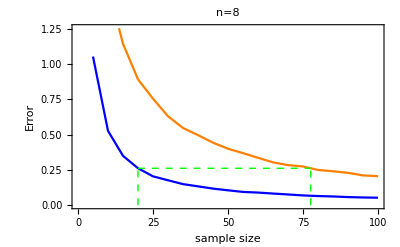

```mathematica
vSampleSize=Table[i,{i,5,100,5}];
lVariance=ParallelTable[fVarianceEstimator[8,10000,i,1],{i,vSampleSize}];
lVariance2=ParallelTable[fVarianceEstimator[8,10000,i,0],{i,vSampleSize}];
f2=Interpolation[Thread[{vSampleSize,lVariance}]];
h2=Interpolation[Thread[{vSampleSize,lVariance2}]];
l8=Table[{n,NSolve[h2[x]==f2[n],x][[1,1,2]]},{n,5,25,5}]
aSolve=NSolve[h2[x]==f2[20],x][[1,1,2]];
g2=ListLinePlot[{Thread[{vSampleSize,lVariance}],Thread[{vSampleSize,lVariance2}]},Frame->{True,True,False,False},FrameLabel->{"sample size","Error"},BaseStyle->{FontSize->14},PlotStyle->{Blue,Orange,Red},PlotLabel->"n=8",Epilog->{{Thick,Green,Dashed,Line[{{20,f2[20]},{aSolve,h2[aSolve]}}]},{Thick,Green,Dashed,Line[{{20,0},{20,f2[20]}}]},{Thick,Green,Dashed,Line[{{aSolve,0},{aSolve,h2[aSolve]}}]}}]
```

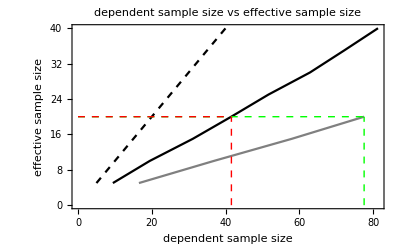

```mathematica
g3=Show[ListLinePlot[{Reverse/@l6,Reverse/@l8},Frame->{True,True,False,False},FrameLabel->{"dependent sample size","effective sample size"},BaseStyle->{FontSize->14},PlotStyle->{Black,Gray},PlotLabel->"dependent sample size vs\n effective sample size",Epilog->{{Thick,Dashed,Green,Line[{{aSolve,0},{aSolve,20}}],Line[{{0,20},{aSolve,20}}]},{Thick,Dashed,Red,Line[{{bSolve,0},{bSolve,20}}],Line[{{0,20},{bSolve,20}}]}}],Plot[x,{x,5,40},PlotStyle->{Dashed,Black}]]
```

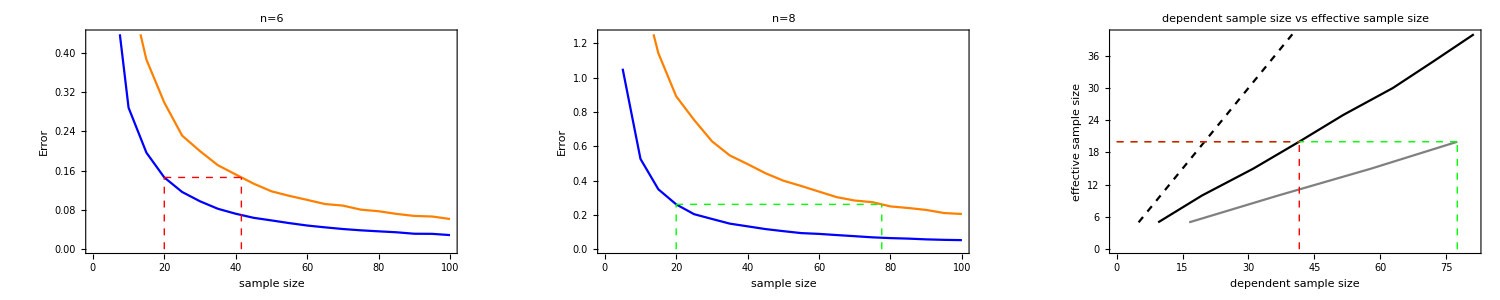

```mathematica
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->1500]
```

```mathematica
Export["MCMC_dependentCorrelationDie.pdf",gFinal]
```

MCMC_dependentCorrelationDie.pdf